```mathematica
RatioPenalty[x_,y_,u_,v_]:=1+u/x+v/y(*(x/y-u/v)+(y/x-v/u)*)
```

```mathematica
Plot3D[{
RatioPenalty[x,y,1,1],
RatioPenalty[x,y,0.1,0.5]
},{x,0,1},{y,0,1},
PlotRange->{0,10},
ClippingStyle->None,
PlotPoints->50,
PlotStyle->{Yellow,Blue}]
```

-Graphics3D-

```mathematica
f[x_]:= Norm[x]
D[f[x]^2,x]
```

2 Norm[x] Norm'[x]

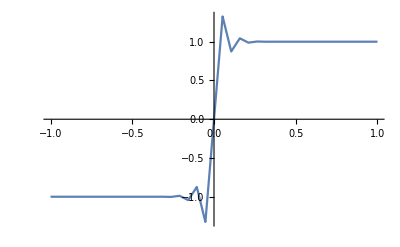

```mathematica
Plot[ Norm'[x],{x,-1,1}]
```

```mathematica
before = {0.5,0.5};
after[{x_,y_},{u_,v_}]:=(1+v/y+u/x)*Norm[{x,y}-{u,v}]^2
Plot3D[{after[{x,y},before]},{x,0,1},{y,0,1},
PlotRange->{0,1},
PlotPoints->100,
MeshFunctions->{#3&},
ClippingStyle->None]
```

-Graphics3D-

```mathematica
w={w1,w2,w3};
h={h1,h2,h3};
Minimize[Norm[{x,y}-{1,1}],(x-0.5)*(y-0.49)==0,{x,y}]
```

{0.5,{x→0.5,y→0.999942}}

```mathematica
Grad[(1-w.h)^2,{w1,w2,h1,h2}]
```

{-2 h1 (1-h1 w1-h2 w2),-2 h2 (1-h1 w1-h2 w2),-2 w1 (1-h1 w1-h2 w2),-2 w2 (1-h1 w1-h2 w2)}

```mathematica
D[(1-w.h)^2,{{w1,w2,w3,h1,h2,h3},2}]//Simplify//MatrixForm
```

(2 h1^2 | 2 h1 h2 | 2 h1 h3 | 2 (-1+2 h1 w1+h2 w2+h3 w3) | 2 h1 w2 | 2 h1 w3
2 h1 h2 | 2 h2^2 | 2 h2 h3 | 2 h2 w1 | 2 (-1+h1 w1+2 h2 w2+h3 w3) | 2 h2 w3
2 h1 h3 | 2 h2 h3 | 2 h3^2 | 2 h3 w1 | 2 h3 w2 | 2 (-1+h1 w1+h2 w2+2 h3 w3)
2 (-1+2 h1 w1+h2 w2+h3 w3) | 2 h2 w1 | 2 h3 w1 | 2 w1^2 | 2 w1 w2 | 2 w1 w3
2 h1 w2 | 2 (-1+h1 w1+2 h2 w2+h3 w3) | 2 h3 w2 | 2 w1 w2 | 2 w2^2 | 2 w2 w3
2 h1 w3 | 2 h2 w3 | 2 (-1+h1 w1+h2 w2+2 h3 w3) | 2 w1 w3 | 2 w2 w3 | 2 w3^2)

```mathematica
w
```

```mathematica
D[Sum[Subscript[w, i]*Subscript[h, i]*Subscript[w, j]*Subscript[h, j],{i,0,n},{j,0,n}]]
```

∑_(i=0)^n ∑_(j=0)^n h_i h_j w_i w_j